## Scatter Plot

## Parametrized scatter plots for a mathematical function

Define the mathematical function that will be evaluated
f(x) = a 1/x-x^2×b

```mathematica
mfunc[arg_,pars_]:=pars[[1]]*1/arg-arg^2*pars[[2]];
```

## Graphical representation of the mathematical function

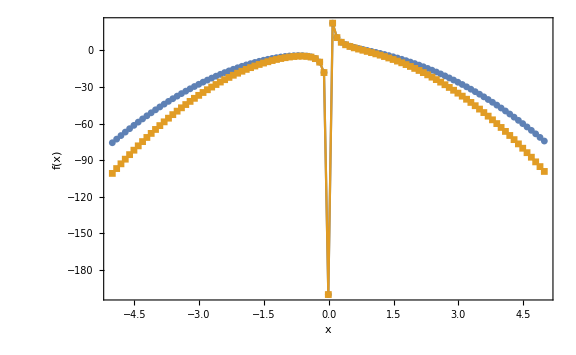

```mathematica
listOfParams={{2,3},{2,4}};
plotTable[params_]:=Table[Table[{x,mfunc[x,params[[id]]]},{x,-5.01,5.01,0.1}],{id,1,Length[params]}];
ListPlot[plotTable[listOfParams],Joined->True,PlotMarkers->{Automatic, Small},ImageSize->Large,Frame->True,Axes->True,FrameStyle->Directive[Black,Thick],FrameLabel->{"x","f(x)"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"}]
```